# Plots for paper

### Clear all variables

```mathematica
Remove["GLO`*"];
Remove["Global`*"];
```

### Import GLO package

```mathematica
Get["~/Documents/Wolfram Mathematica/GLO/functions/GLO.wl"];
```

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16}];
SetOptions[ListPlot,BaseStyle->{FontSize->16}];
```

### Maximum renyi-2

```mathematica
S2max[s_,r_]:=Min[r,1-r]Log@Cosh[2s];
```

### Analytic page curve up to order r^dmax

```mathematica
S2[s_,r_,dmax_:20]:=With[{t2=Tanh[2s]^2,m=Min[r,1-r]},
m Log@Cosh[2s]+∑_(d=2)^dmax m^d∑_(l=Ceiling[d/2])^(d-1) (-1)^(d-l)/l t2^l Binomial[2l-1,l-1]Binomial[l,d-l-1](2l-d+1)/((d-1)d)
];
```

### Exact result for when r=1/2

```mathematica
S2half[s_]:=Log@Cosh@s;
```

### Max renyi-2 minus average renyi-2 at r=1/2

```mathematica
pageCorrection[s_]:=1/2 Log[1+Tanh[s]^2];
```

## Qualitative

```mathematica
s=.75;
```

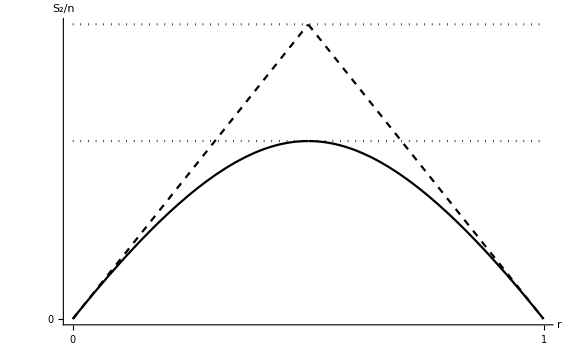

```mathematica
Plot[
{
S2max[s,r],S2[s,r],
S2half[s],S2half[s]+pageCorrection[s]
},
{r,0,1},
PlotRange->All,
AxesLabel->{"r","S_2/n"},
ImageSize->Large,
AxesStyle->Black,
Ticks->{{0,1},{0}},
PlotStyle->{{Black,Dashed},{Black},{Black,Dotted},{Black,Dotted}}
]
```

### Table

```mathematica
Export[
"~/Desktop/qualitative.dat",
Join[
{{"r","Squal"}},
Table[{r,S2[s,r]},{r,0,1,.001}]
],
"Table","FieldSeparators"->" "
]
```

~/Desktop/qualitative.dat

## Data

```mathematica
n=50;
rs=Range[0,1,.02];
partitionSize[n_,r_]:=Round[r n]//N;
squeeze:=Table[s,n];
iters=300;
```

```mathematica
data=Table[
{
r,
Mean@Table[
1/n renyi2EntropyOfLeftPartition[initialSqueezedState@squeeze~applyByCongruence~haarModeMatrix@n,partitionSize[n,Min[r,1-r]]],
iters
]
},
{r,rs}
];
```

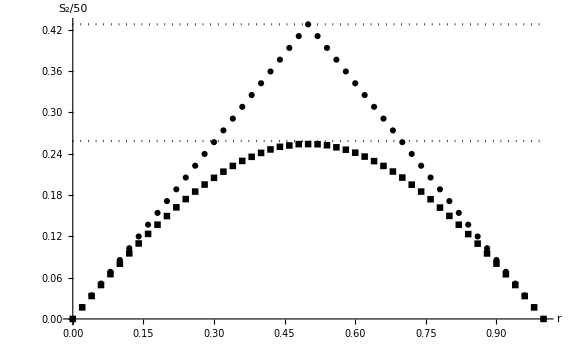

```mathematica
ListPlot[
{
Table[{r,S2max[s,r]},{r,rs}],
data,
Table[{r,S2half[s]},{r,rs}],
Table[{r,S2half[s]+pageCorrection[s]},{r,rs}]
},
PlotRange->All,
AxesLabel->{"r","S_2/50"},
ImageSize->Large,
AxesStyle->Black,
PlotStyle->{{Black,Dotted},{Black},{Black,Dotted},{Black,Dotted}},
Joined->{False,False,True,True},
PlotMarkers->{Automatic,Automatic,None,None}
]
```

### Table

```mathematica
Export[
"~/Desktop/quantitative.dat",
Join[
{{"r","Squan","Smax"}},
Table[{rs[[i]],data[[i]][[2]],S2max[s,rs[[i]]]},{i,Length@rs}]
],
"Table","FieldSeparators"->" "
]
```

~/Desktop/quantitative.dat